```mathematica
<<"C:\\Users\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\SpectraFitting.m"
```

## Data input and grooming

Directory where spectra reside. Should be tab separated files, but CSV will probably also work.

```mathematica
DataDir="C:\\Users\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\Example Data\\XPS";
```

```mathematica
XPSPath="C:\\Users\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\Example Data\\XPS\\2014-06-17_10048_76_77_79_synchotronsamples.xlsx";
```

```mathematica
XPSSpecs=GetSpec[XPSPath,"Excel XPS","C1s"];
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

11 spectra in all.

Importing Sheet C1s Scan J

Importing Sheet C1s Scan I

Importing Sheet C1s Scan H

Importing Sheet C1s Scan G

Importing Sheet C1s Scan F

Importing Sheet C1s Scan E

Importing Sheet C1s Scan D

Importing Sheet C1s Scan C

Importing Sheet C1s Scan B

Importing Sheet C1s Scan A

Importing Sheet C1s Scan

Formatting XPS Spectra

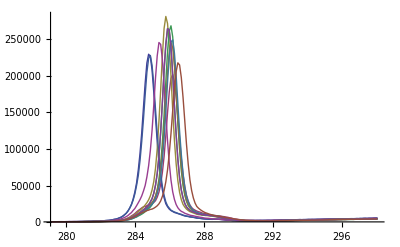

```mathematica
ListLinePlot[XPSSpecs,PlotRange->All]
```

```mathematica
coordlist=CoordInit[XPSSpecs,285,5]
```

{{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}}}

```mathematica
PickGuesses[XPSSpecs,coordlist]
```

Part::partw: Part 2 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 3 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 4 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{,,,,,,,,,,}

```mathematica
coordlist
```

{{{285,1000},{280.7,1300.},{290.82,2600.},{290.28,2600.}},{{286.48,4000.},{565/2,1000},{292.01,2600.},{290.84,3000.}},{{285.94,3350.},{565/2,1000},{291.56,2250.},{290.61,2350.}},{{286.48,4100.},{565/2,1000},{291.29,2250.},{290.66,2250.}},{{284.86,3050.},{281.22,1200.},{291.11,2700.},{290.48,2450.}},{{285,1000},{281.49,1500.},{291.15,2250.},{290.43,2450.}},{{285.4,3100.},{565/2,1000},{291.38,2350.},{290.75,2000.}},{{285,1000},{565/2,1000},{291.29,2250.},{290.66,1950.}},{{286.25,6150.},{565/2,1000},{291.29,2300.},{290.43,2550.}},{{285,1000},{565/2,1000},{291.47,2450.},{290.79,2250.}},{{285,1000},{565/2,1000},{291.74,2500.},{290.88,2800.}}}

```mathematica
data=ChopBoth[XPSSpecs,coordlist][[1]];
```

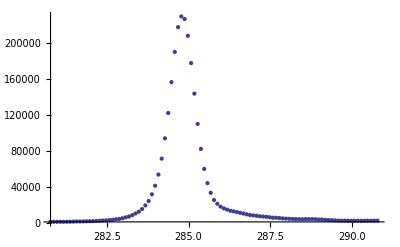

```mathematica
ListPlot[data,PlotRange->All]
```

## Peak fitting XPS data

Fit is not very good leaving everything free.

```mathematica
nlm=Model[data,2];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

217423. ⅇ^(-2.99953 (-284.808+x)^2)+18855.8 ⅇ^(-4.73186×10^-6 (227.113+x)^2)

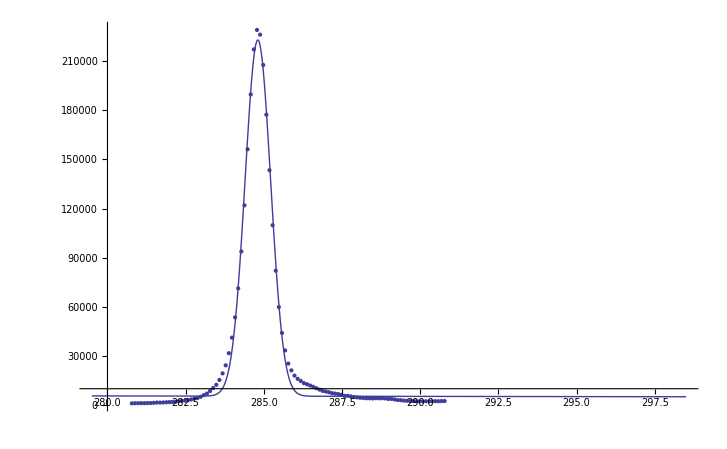

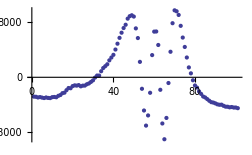

Can also use Voigt profiles. More parameters, trickier to fit. Prone to finding local minima. Not recommended yet.

(221494. 2^(-4.79661 (-284.803+x)^2))/(1-0.48443 (-284.803+x)^2)+(17836. 2^(-0.0489499 (-67.0585+x)^2))/(1-0.0451856 (-67.0585+x)^2)+(948.559 2^(-0.029004 (-20.4369+x)^2))/(1-0.0272774 (-20.4369+x)^2)

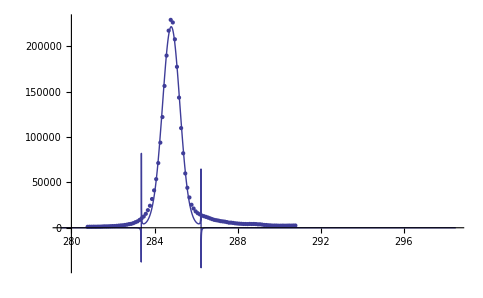

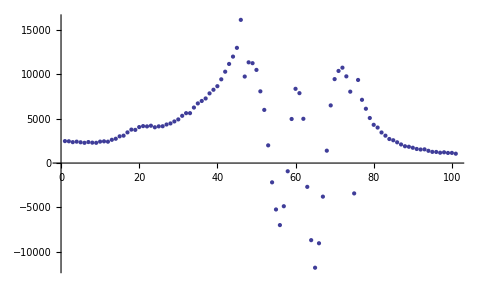

```mathematica
nlm=VoigtModel[data,3];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

Can used knowledge of peak positions with FixedPeaksModel:

279.065 ⅇ^(-0.0000577052 (-288.102+x)^2)+444.521 ⅇ^(-0.0000112515 (-287.002+x)^2)+12323. ⅇ^(-0.128642 (-285.802+x)^2)+213264. ⅇ^(-3.24599 (-284.802+x)^2)

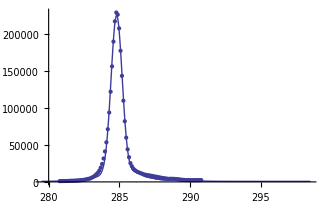

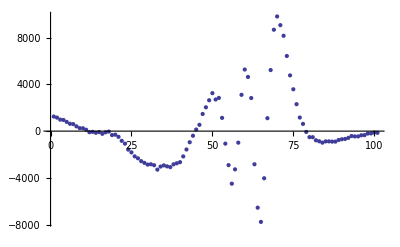

```mathematica
nlm=FixedPeaksModel[data,{-1,0,1.2,2.3}];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

Can used knowledge of peak positions with FixedPeaksModel:

(0.0248885 2^(0.0000582317 (-938.197+x)^2))/(1+0.0000593864 (-938.197+x)^2)

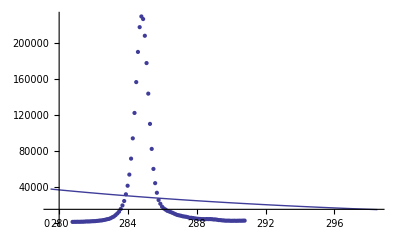

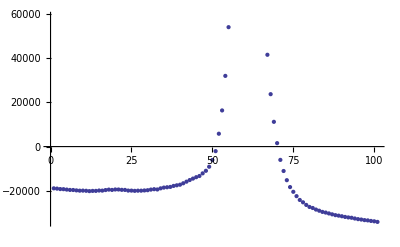

```mathematica
nlm=FixedPeaksVoigtModel[data,{0}];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

(1066.75 2^(-60.6086 (-319.713+x)^2))/(1-60.5002 (-319.713+x)^2)+(1.07972×10^6 2^(-0.00330268 (-318.613+x)^2))/(1-0.0000242776 (-318.613+x)^2)+(4.24744×10^6 2^(-0.00451086 (-317.413+x)^2))/(1-0.0044639 (-317.413+x)^2)+(531686. 2^(-0.125433 (-316.413+x)^2))/(1-0.125212 (-316.413+x)^2)

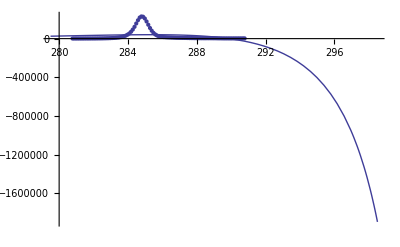

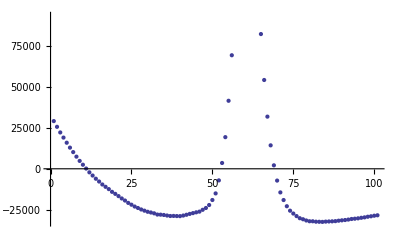

```mathematica
nlm=FixedPeaksVoigtModel[data,{-1,0,1.2,2.3}];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

## Multi-peak fitting with generated data

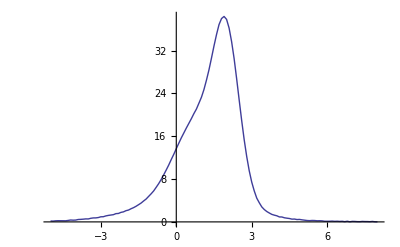

25.1057 ⅇ^(-1.99508 (-1.99902+x)^2)+16.1163 ⅇ^(-0.497021 (-0.990415+x)^2)+3.85703 ⅇ^(-0.116134 (-0.489983+x)^2)

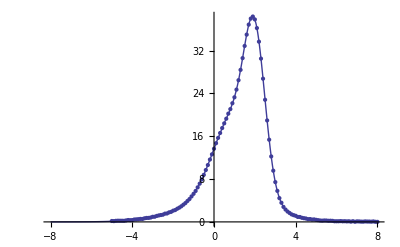

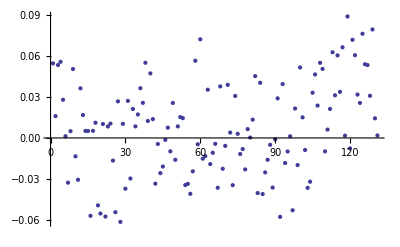

```mathematica
data2=Table[{x,gfn[4,1,1,x]+gfn[5,2,0.5,x]+gfn[2,0.5,2,x]+0.1*RandomReal[]//N},{x,-5,8,0.1}];
ListLinePlot[data2]
nlm2=Model[data2,3];
nlm2[x]
Show[Plot[nlm2["Function"][x],{x,-8,8},PlotRange->All],ListPlot[data2,PlotRange->All]]
ListPlot[nlm2["FitResiduals"]]
```

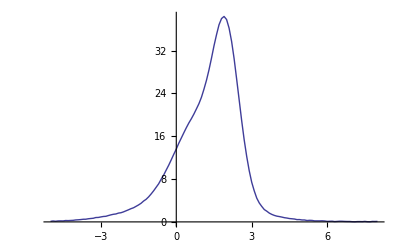

24.9801 ⅇ^(-2.01044 (-1.99924+x)^2)+16.1531 ⅇ^(-0.495882 (-0.99924+x)^2)+3.91041 ⅇ^(-0.118018 (-0.49924+x)^2)

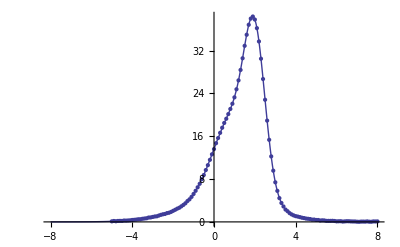

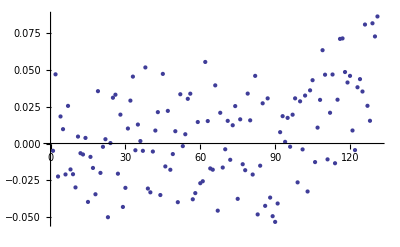

```mathematica
data2=Table[{x,gfn[4,1,1,x]+gfn[5,2,0.5,x]+gfn[2,0.5,2,x]+0.1*RandomReal[]//N},{x,-5,8,0.1}];
ListLinePlot[data2]
nlm2=FixedPeaksModel[data2,{1,-0.5,0}];
nlm2[x]
Show[Plot[nlm2["Function"][x],{x,-8,8},PlotRange->All],ListPlot[data2,PlotRange->All]]
ListPlot[nlm2["FitResiduals"]]
```

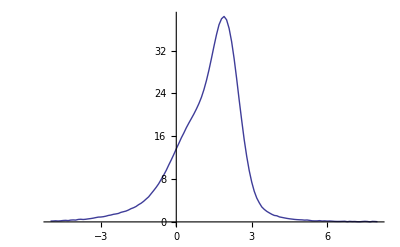

(33.4066 2^(-2.2467 (-1.90903+x)^2))/(1-0.135812 (-1.90903+x)^2)+(1.57346×10^-11 2^(-0.0664325 (-0.909032+x)^2))/(1+0.0354018 (-0.909032+x)^2)+(16.4409 2^(-0.0474042 (-0.409032+x)^2))/(1+1.00537 (-0.409032+x)^2)

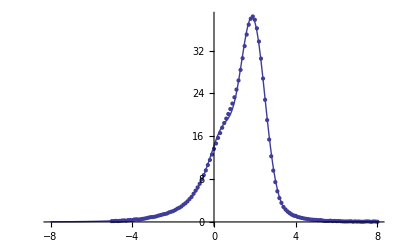

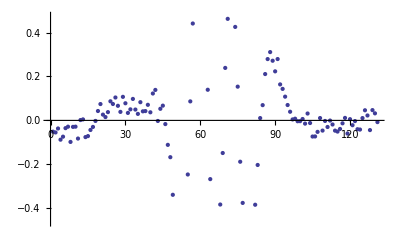

```mathematica
data2=Table[{x,gfn[4,1,1,x]+gfn[5,2,0.5,x]+gfn[2,0.5,2,x]+0.1*RandomReal[]//N},{x,-5,8,0.1}];
ListLinePlot[data2]
nlm2=FixedPeaksVoigtModel[data2,{1,-0.5,0}];
nlm2[x]
Show[Plot[nlm2["Function"][x],{x,-8,8},PlotRange->All],ListPlot[data2,PlotRange->All]]
ListPlot[nlm2["FitResiduals"]]
```